```mathematica
σ0 = 0.5*32.77*(1/0.3894)
mvN[r_, γ_, Qs0_, Λ_, ec_]:= σ0(1- Exp[-((r^2 Qs0^2)/4)^γ Log[1/(r Λ)+ ec*E]]) ;

Nc = 3.0;
CF = (Nc^2-1)/(2 Nc);
Rp = 1/0.4; 
Qs2[b_] := (4π (0.25)^2 CF)/Nc Exp[-b^2/(2 Rp^2)]
mvB[r_, b_, γ_, Qs0_, Λ_, ec_]:= (1- Exp[-((r^2 Qs2[b])/4)^γ Log[1/(r Λ)+ ec*E]]) ;
```

42.0776

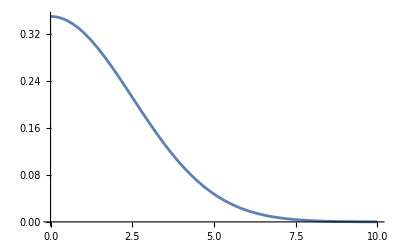

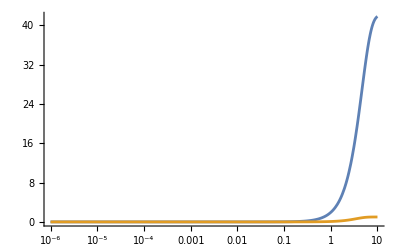

```mathematica
Plot[Qs2[b], {b,0,10}]
LogLinearPlot[{mvN[r, 1.13, Sqrt[0.15], 0.241, 1],mvB[r, 2, 1.13, Sqrt[0.15], 0.241, 1]} , {r,10^-6, 10}, PlotRange->All]
```

```mathematica
tFB[p_, Q_, z_, ia_, ib_,ic_,id_] := NIntegrate[(p r)^ic(Q Sqrt[z(1-z)] r)^id r BesselJ[ia, p r]*BesselK[ib, Q*Sqrt[z*(1-z)] r] mvN[r, 1.13, Sqrt[0.15], 0.241, 1], {r,10^-6, 3.3}];

tFBQs[p_, Q_, z_, ia_, ib_,ic_,id_, Qs_] := NIntegrate[(p r)^ic(Q Sqrt[z(1-z)] r)^id r BesselJ[ia, p r]*BesselK[ib, Q*Sqrt[z*(1-z)] r] mvN[r, 1.13, Qs, 0.241, 1], {r,10^-6, 3.3}];

tFFB[p_, Q_, z_, Δ_, ia_, ib_,ic_,id_] := NIntegrate[(p r)^ic(Q Sqrt[z(1-z)] r)^id r BesselJ[ia, p r]* BesselJ[1, b Δ]*BesselK[ib, Q*Sqrt[z*(1-z)] r] mvB[r,b,  1.13, Sqrt[0.15], 0.241, 1], {r,10^-6, 3.3}, {b, 10^-6, 3.3}];

(*bFB[Δ_, r_] := NIntegrate[b  BesselJ[0, Δ b]mvB[r, b,  1.13, Sqrt[0.15], 0.241, 1], {b,10^-6, 3.3}];*)

bFB[Δ_, r_] := NIntegrate[b  mvB[r,b,  1.13, Sqrt[0.15], 0.241, 1], {b,10^-6, 3.3}];

tFBRiemann[p_, Q_, z_, ia_, ib_,ic_,id_] := 0.01*Sum[Exp[2u](p Exp[u])^ic(Q Sqrt[z(1-z)] Exp[u])^ic  BesselJ[ia, p Exp[u]]*BesselK[ib, Q*Sqrt[z*(1-z)] Exp[u]] mvN[Exp[u], 1.13, Sqrt[0.15], 0.241, 1], {u,-13, 2, 0.01}];
```

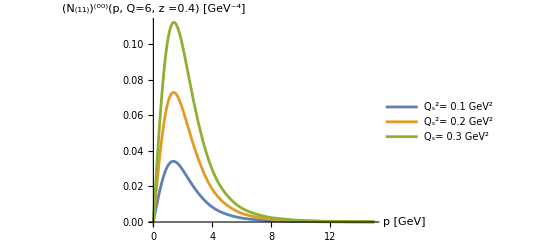

```mathematica
(*Plot[{tFB[p, 6, 0.4, 1,1,0,0, ], tFB[p, 7.5, 0.4, 1,1,0,0], tFB[p, 8, 0.4, 1,1,0,0]}, {p, 0,15}, PlotRange->All]*)
Plot[{tFBQs[p, 6, 0.4, 1,1,0,0, Sqrt[0.1]], tFBQs[p, 6, 0.4, 1,1,0,0,Sqrt[0.2]], tFBQs[p, 6, 0.4, 1,1,0,0,Sqrt[0.3]]}, {p, 0,15}, PlotRange->All, PlotLegends->{"Q_s^2= 0.1 GeV^2", "Q_s^2= 0.2 GeV^2", "Q_s= 0.3 GeV^2"}, AxesLabel->{"p [GeV]", "(N_(11))^(00)(p, Q=6, z =0.4) [GeV^-4]"}]

(*LogPlot[{bFB[Δ, 0.01], bFB[Δ, 0.1], bFB[Δ, 1.0], bFB[Δ, 3.3]}, {Δ, 0.3,0.9}, PlotRange->All, PlotLegends->{"r = 0.01 GeV^-1", "r = 0.1 GeV^-1", "r = 1 GeV^-1", "r = 3.3 GeV^-1"}]*)

(*LogLinearPlot[{bFB[0,r]}, {r, 10^-3,3.3}, PlotRange->All, PlotLegends->{}]*)
(*Plot[{tFBRiemann[p, 6, 0.4, 1,1,0,0], tFBRiemann[p, 7.5, 0.4, 1,1,0,0], tFBRiemann[p, 9, 0.4, 1,1,0,0]}, {p, 0,15}, PlotRange->All]*)
```

```mathematica
αem = 1/137;
ATT[p_, z_, Q_] := (4 αem (1/9 + 1/9 + 4/9)*9*Q^2*z*(1-z) (z^2+ (1-z)^2))/(2π)^4(tFB[p, Q, z, 1,1,0,0])^2;
ALL[p_, z_, Q_] := (8 αem (1/9 + 1/9 + 4/9)*9*Q^2*z^3*(1-z)^3)/(2π)^4(tFB[p, Q, z, 0,0,0,0])^2;
xsec[p_,Q_, z_, y_] := αem/(4 π^2 Q^2 y)(
(1+(1-y)^2) ATT[p, z,Q] + 4(1-y) ALL[p, z,Q]
)
```

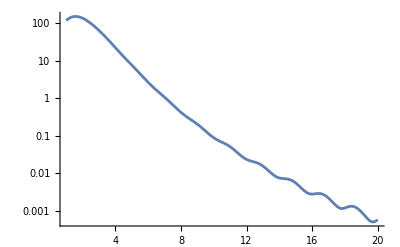

```mathematica
ty=0.6;
tQ=6; 
tz=0.4;
tx=0.01;

LogPlot[(2π)^3/4((pT*ty)/(tx tz(1-tz)))xsec[pT, tQ, tz, ty]0.389*10^9, {pT, 1,20}, PlotRange->All] (* xsec in pb *)
```

```mathematica
Log[3.3]//N
```

1.19392

```mathematica
NInte
```

```mathematica
0.0042 *4/9*0.648^2*(330^2- 319^2)
```

5.5957